```mathematica
<<ACPackages`
<<ACPackages`Master`
```

```mathematica
SetWorkDir["2010.07.09\\chi1.1"]
```

D:\programs\icmm\tormagn\2010.07.09\chi1.1

```mathematica
SetWorkDir[]
```

d:\home\Anton\programs\tormagn

```mathematica
SetWorkDir["2010.06.16"]
```

```mathematica
$HistoryLength=0;
```

#### Разбор логов

```mathematica
text=Import["message.dat","Text"];
```

```mathematica
StrMsg[msg_String]:="(?s)(message of proc#(\\d+) at )?t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>msg
StrChg[par_String]:=StrMsg[par<>" was changed to"]
```

```mathematica
StrChg[par_String]:="t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>par<>" was changed to";
```

```mathematica
Rmt=StringCases[text,RegularExpression[StrChg["Rm"]]:>ToExpression["$3"]];
```

```mathematica
StringCases[text,RegularExpression[StrMsg["(.*?)"]]:>"$0"]//Length
```

```mathematica
StringCases[text,RegularExpression[StrChg["rc"]]:>"$3"]
```

{0.3500,0.3000,0.2500,0.2000,0.1500,0.1000,0.0500,0.0000}

```mathematica
cs=StringCases[text,RegularExpression[StringJoin["(?s)(",StrChg["rc"],")?(.+?)(?=(",StrChg["rc"],")|$)"]]:>"$0"];cs={StringCases[#,RegularExpression[StrChg["rc"]]->"$3"],StringCases[#,RegularExpression[StrChg["Rm"]]->"$3"],StringCases[#,RegularExpression[StrMsg["snap is done"]]->"$5"]}&/@cs;
TableForm[{#⟦1⟧,#⟦3,-1⟧}&/@cs]
```

| 137638
0.3500 | 201312
0.3500 | 161266

```mathematica
cs
```

{{{},{10.9966,11.4343,11.7236,11.9442,12.1194,12.2729,12.4075,12.5332,12.6571,12.7401,12.7908,12.7510,12.5333,12.1309,11.6398,11.1766,10.6961,10.2260,9.7764,9.3507,8.9304,8.5516,8.1402,7.7863,7.4202,7.1023,6.7988,6.2166,5.9480,5.6778,5.4309,5.1913,4.9610,4.7428,4.5300,4.3290,4.1404,3.9581,3.7870,3.6165,3.4558,3.3054,3.1624,3.0246,2.8909,2.7743,2.6500,2.5345,2.4256,2.3182,2.2155,2.1171,2.0265,1.9381,1.8550,1.6965,1.6224,1.5515,1.4830,1.4171,1.3557,1.2966,1.2392,1.1845,1.1328,1.0822,1.0342,0.9884,0.9461,0.9042,0.8650,0.8267,0.7914,0.7580,0.6927,0.6622,0.6336,0.6064,0.5800,0.5551,0.5311,0.5078,0.4859,0.4628,0.4425,0.4231,0.4043,0.3865,0.3694,0.3528,0.3373,0.3227,0.3092,0.2956,0.2827,0.2707},{1383,2757,4129,5503,6879,8255,9633,11007,12383,13761,15133,16509,17884,19256,20631,22009,23385,24763,26141,27519,28896,30268,31640,33012,34383,35758,37132,38504,39875,41255,42632,44006,45381,46761,48141,49518,50893,52270,53645,55025,56406,57782,59158,60534,61911,63290,64666,66040,67416,68791,70166,71541,72920,74297,75675,77055,78434,79810,81186,82562,83938,85314,86690,88067,89444,90821,92200,93577,94956,96332,97709,99090,100466,101842,103217,104598,105974,107350,108726,110102,111478,112854,114229,115606,116982,118358,119733,121111,122488,123863,125240,126615,127994,129370,130745,132125,133499,134879,136257,137638}},{{0.3500},{0.2328,11.2305,12.1942,12.6726,12.9505,13.1202,13.2427,13.3423,13.4277,13.5038,13.5758,13.6413,13.6999,13.7523,13.8002,13.8427,13.8627,13.8133,13.6001,13.1890,12.6700,12.1095,11.5854,11.0890,10.6071,10.1414,9.7067,9.2869,8.8879,8.4898,8.1150,7.7668,7.4261,7.1007,6.7897,6.4957,6.2130,5.9402,5.6796,5.4233,5.1880,4.9585,4.7451,4.5453,4.3486,4.1581,3.9780,3.8073,3.6394,3.4777,3.3263,3.1801,3.0421,2.9082,2.7820,2.5451,2.4337,2.3263,2.2243,2.1230,2.0300,1.9433,1.8599,1.7785,1.6983,1.6251,1.5549,1.4865,1.4186,1.3570,1.2978,1.2411,1.1860,1.1335,1.0825,1.0357,0.9462,0.9050,0.8656,0.8269,0.7900,0.7549,0.7228,0.6914,0.6613,0.6318,0.6045,0.5772,0.5519,0.5282,0.5052,0.4831,0.4619,0.4421,0.4228,0.4045,0.3864},{53885,66344,67716,69088,70460,71832,73202,74572,75942,77315,78694,80067,81443,82817,84191,85558,86929,88304,89681,91059,92438,93814,95190,96565,97945,99322,100697,102077,103454,104830,106205,107583,108958,110335,111713,113093,114473,115854,117231,118609,119988,121365,122745,124124,125500,126877,128258,129635,131014,132391,133772,135150,136527,137907,139288,140665,142045,143425,144805,146186,147562,148939,150320,151695,153075,154455,155835,157214,158591,159970,161346,162723,164103,165484,166860,168237,169617,170998,172375,173755,175135,176514,177890,179267,180646,182022,183399,184779,186157,187536,188912,190288,191665,193043,194423,195803,197182,198558,199933,201312}},{{0.3500},{0.3324,0.2854,0.2454},{53905,107322,161266}}}

```mathematica
StringCases[text,RegularExpression["t=(10(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=(\\d+(\\.\\d+)?) sec:\nsnap is done"]:>{"$1","$3","$4"}]
```

{{10.0000,137638,12200},{10.0000,201312,11894.1}}

```mathematica
StringReplace[StringDrop["="<>StringJoin[#<>"+"&/@((%14)^ᵀ)[[2]]],-1],"."->","]
```

=137638+201312

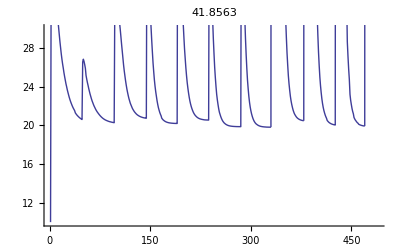

41.8563

```mathematica
ListPlot[Rmt,PlotRange->{10,30},PlotLabel->Last[Rmt],Joined->True]
Last[Rmt]
```

```mathematica
Select[Transpose[{Rmt,RotateLeft[Rmt]}],First[#]/Last[#]<1/2&]
```

{{10,37.2238}}

#### Графики по времени

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[{#⟦1,1⟧,#⟦2⟧}&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

```mathematica
PrintRange[{First[#],Max[Last[#]]}&/@lv,All,PlotLabel->"Maximum of stream velocity"]
```

```mathematica
Export["energy5.dat",Transpose@Join[{ltm},Map[Last,{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz},{2}]]]
```

```mathematica
PrintRange[dif[ltm],All,PlotLabel->"Time step"]
PrintRange[{#⟦1⟧/3,#⟦2⟧}&/@(mqvx+mqvy+mqvz)]
```

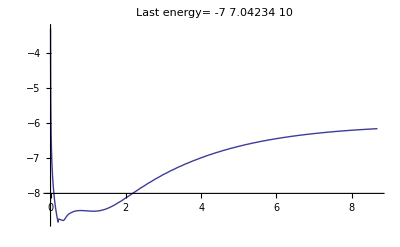

```mathematica
len=Transpose[Select[Import["energy.dat","Table"],(0<First[#])&]];
ltm=First[len];(*PrintRange[dif[ltm],All,PlotLabel->"Time step"]*)
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz}=Transpose[{ltm,#}]&/@Drop[len,2];
(*PrintRange[{#⟦1⟧/3,#⟦2⟧}&/@(mqvx+mqvy+mqvz)]*)
(*PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqAx+mqAy+mqAz),All,PlotLabel->"Last energy="<>ToString[Last[Last[mqAx+mqAy+mqAz]]]]*)
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqBx+mqBy+mqBz),All,
PlotLabel->"Last energy="<>ToString[Last[Last[mqBx+mqBy+mqBz]]]]
```

```mathematica
HarmClearance[l_]:=Divide@@Take[Sort[Take[Abs@Fourier@l,Ceiling[Length[l]/2]]],-2]
```

```mathematica
out=.;ReadBinarySnapFiles["ponom_","_02282.snp",6,out,PrintInfo->None];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,2,2},NumberOfRefs->4];
{Bx,By,Bz}=rotc[Sequence@@Take[out,-3],3];
PrintRange[WithoutFict@Bx⟦10,All,25⟧]
PrintRange[Take[Abs@Fourier@WithoutFict@Bx⟦15,All,15⟧,14]]
-10Log[10,HarmClearance[WithoutFict@Bx⟦13,All,8⟧]]
```

5.61504

```mathematica
EstimateBoundary/@{Bx,By,Bz}
```

{63.4129,410.987,127.973}

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{{mqvx,mqvy,mqvz,mqp},{"Mean quadratic of vr","Mean quadratic of vϕ","Mean quadratic of vz","Mean quadratic of p"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]&/@{mqAx,mqAy,mqAz},{"Mean quadratic of Ar","Mean quadratic of Aϕ","Mean quadratic of Az"}}]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[Abs[l⟦2⟧]]/2}],#]&/@{mdAx,mdAy,mdAz},{"Difference of Ar","Difference of Aϕ","Difference of Az"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{dif[Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]]&/@{mqBx,mqBy,mqBz},{"Mean quadratic of Br","Mean quadratic of Bϕ","Mean quadratic of Bz"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[Abs[l⟦2⟧]]}],#]&/@{mAx,mAy,mAz},{"Maximum of Ar","Maximum of Aϕ","Maximum of Az"}}]
```

```mathematica
PrintRange[mBx]
```

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[10,Abs[l⟦2⟧]]}],#]&/@{mBx,mBy,mBz},{"Maximum of Br","Maximum of Bϕ","Maximum of Bz"}}]
```

#### Чтение из файлов

```mathematica
Remove[PrintInfo]
```

```mathematica
{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0},NumberOfRefs->4];
```

```mathematica
out=.;ReadBinarySnapFile["screw.dmp",8,out,PrintInfo->Debug];
```

{1,1,2}

{0.,0,32,32,32,1000.}

Length of read from binary=508288 and size of it=2033152 bytes

ghost=3

```mathematica
out=.;ReadBinarySnapFile["velocity.snp",4,out,PrintInfo->Debug];
```

{1,1,1}

{0.,0,64,64,64,3.14}

Length of read from binary=1372000 and size of it=5488000 bytes

ghost=3

```mathematica
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,1,1},NumberOfRefs->4];
```

```mathematica
out=.;ReadBinarySnapFile["screw_32_162.snp",6,out,PrintInfo->Debug];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{4,2,4},NumberOfRefs->4];
Print[bounds];
```

```mathematica
If[Length[out]>6,out=Take[out,{2,-2}]];
```

```mathematica
out=.;ReadBinarySnapFiles["screw",".dmp",8,out,PrintInfo->None];
(*{vx,vy,vz,Ax,Ay,Az}=out;*)
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{4,4,1},NumberOfRefs->0];
```

```mathematica
out=.;ReadBinarySnapFile["velocity.snp",5,out,PrintInfo->None];
```

Выделение внутренней области

```mathematica
GetInner[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(node/.b_:>BitAnd[b,8])/8#&/@Transpose[ar]],2,(node/.b_:>BitAnd[b,8])/8 ar,_,$Failed]]
```

```mathematica
GetVacuum[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(1-(node/.b_:>BitAnd[b,8])/8)#&/@Transpose[ar]],2,(1-(node/.b_:>BitAnd[b,8])/8)ar,_,$Failed]]
```

```mathematica
{vxs,vys,vzs,ps,nuts}=GetInner/@{vx,vy,vz,p,nut};
```

```mathematica
{Bx,By,Bz}=rotd[Sequence@@Take[out,-3],3];
(*{jx,jy,jz}=rotd[Bx,By,Bz,3];*)
```

#### Проверка совпадения

```mathematica
{p1,vx1,vy1,vz1,Axm1,Aym1,Azm1,nutm1}={p,vx,vy,vz,Axm,Aym,Azm,nutm};
{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}={p,vx,vy,vz,Ax,Ay,Az,nut};
```

```mathematica
{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}=out;
```

```mathematica
{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2}=out;
```

```mathematica
Max/@Abs[{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}-{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2}]
```

{1.,1.5,1.,1.9,1.03193,1.0119,1.03194,1.}

```mathematica
out1=out;
```

```mathematica
{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}={p,vx,vy,vz,Ax,Ay,Az,nut,Axm,Aym,Azm,nutm};
```

```mathematica
Max[Abs[#]]&/@({p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}-{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1,Axm1,Aym1,Azm1,nutm1})
```

{0.,0.,0.,0.,0.,0.,0.,0,0.,0.,0.,0.}

```mathematica
({p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}=={p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1,Axm1,Aym1,Azm1,nutm1})
```

True

```mathematica
(*Brfi[r1_,fi1_,z1_]=ReplaceAll[1/r∂_fi Azi[r,fi,z]-∂_z Ayi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bϕfi[r1_,fi1_,z1_]=ReplaceAll[∂_z Axi[r,fi,z]-∂_r Azi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bzfi[r1_,fi1_,z1_]=ReplaceAll[∂_r Ayi[r,fi,z]-1/r∂_fi Axi[r,fi,z]+1/r Ayi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bzfi[r1_,fi1_,z1_]=ReplaceAll[1/r∂_r (r Ayi[r,fi,z])-1/r∂_fi Axi[r,fi,z],{r->r1,fi->fi1,z->z1}];*)
```

#### Величины

```mathematica
EstimateBoundary[mat_?ArrayQ]:=Block[{Ein,Eb,ds=Dimensions[mat]},
(*Ein=Mean[Flatten@mat⟦2;;-2,All,2;;-2⟧^2];
Eb=√(((Times@@ds) Mean[Flatten@mat^2]-(Times@@(ds-2))Ein)/((Times@@ds)-(Times@@(ds-2))));
Eb/Max[Flatten@Abs@mat]*)
(Max@Abs@Flatten@mat⟦2;;-2,All,2;;-2⟧)/(Max@Abs@Complement[Flatten@mat,Flatten@mat⟦2;;-2,All,2;;-2⟧])
]
```

```mathematica
Max[Abs[Flatten[#]]]&/@(out1-out)
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Max@Abs@√Total[Take[out,{2,4}]^2]
```

1.59816

```mathematica
Total[Flatten[#^2]]&/@out
```

```mathematica
Max/@Abs@out
```

{1.49676,1.49676,1.86638,0.00500015,0.00499985,0.00499985}

```mathematica
√(Mean/@Flatten/@({Bx,By,Bz}^2))
```

{1.21144×10^10,4.3921×10^10,1.37365×10^10}

```mathematica
Mean/@Flatten/@{Bx,By,Bz}
```

{-2.04068×10^8,5.59908,-5.76753×10^8}

```mathematica
(√(Mean/@Flatten/@({Bx,By,Bz}^2)))/(Mean/@Flatten/@{Bx,By,Bz})
```

{-59.3645,7.84432×10^9,-23.817}

#### Простые графики

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,3,19]],PlotRange->All,DisplayFunction->Identity]&,
Take[out,4]]
```

```mathematica
Show2x[ListPlot3D[Transpose[GetVacuum[Cut3D[#,2,7]]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,p}]
```

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,3,19]],PlotRange->All,DisplayFunction->Identity]&,{Bx,By,Bz,out[[1]]}]
```

```mathematica
Table[ListPlot3D[Transpose[Cut3D[Bz,2,i]],PlotRange->All,DisplayFunction->Identity],{i,36}]
```

```mathematica
ListPlot3D[Transpose[Cut3D[out⟦5⟧,2,7]],PlotRange->All,DisplayFunction->Identity]
```

```mathematica
PrintRange[out⟦2,23,All,23⟧]
```

```mathematica
Show2x[ListPlot3D[Cut3D[#,2,4],DisplayFunction->Identity,PlotRange->All]&,{Bx,By,Bz,Last[out]}]
```

```mathematica
(*Show4[ListPlot3D[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,√(vx^2+vy^2+vz^2)}];*)
Show2x[ListPlot3D[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{Ax,Ay,Az,nut}]
Show2x[ListPlot3D[Transpose[Cut3D[WithoutFict[#]]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{Bx,By,Bz,√(Bx^2+By^2+Bz^2)}]
Show2x[ListPlot3D[Transpose[Cut3D[WithoutFict[#]]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{jx,jy,jz,√(jx^2+jy^2+jz^2)}]
```

```mathematica
dist=15;PrintRange[Cut3D[Cut3D[Bx,3,dist],1,dist]]
```

```mathematica
(*ListPlot3D[Transpose[Cut3D[Ay/coor⟦1⟧-PD[Ax,ghost,dx⟦2⟧,2]/coor⟦1⟧]]];
ListPlot3D[Transpose[Cut3D[PD[Ay,ghost,dx⟦1⟧,1]]]];*)
```

#### Интерполированные графики

```mathematica
{vxi,vyi,vzi,pi,Axi,Ayi,Azi,Bxi,Byi,Bzi,jxi,jyi,jzi,nuti}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&/@{vx,vy,vz,p,Ax,Ay,Az,Bx,By,Bz,jx,jy,jz,nut};
```

```mathematica
Show[GraphicsRow[{SectionRZ[vxi,vyi,vzi,0.2 π],SectionRΦ[vxi,vyi,vzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[vxi,vyi,vzi,Mean[bounds⟦1⟧],AspectRatio->Automatic]},Spacings->Scaled[0.]],AspectRatio->1]
```

```mathematica
Show[GraphicsRow[{SectionRZ[Bxi,Byi,Bzi,1.8],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧],AspectRatio->Automatic]},Spacings->Scaled[0.]],AspectRatio->1]
```

```mathematica
Show[GraphicsRow[{SectionRZ[jxi,jyi,jzi,0.3 π],SectionRΦ[jxi,jyi,jzi,Mean[bounds⟦3⟧]],SectionΦZ[jxi,jyi,jzi,Mean[bounds⟦1⟧]]},Spacings->Scaled[0.]],AspectRatio->1,ImageSize->1000]
```

#### Оценки закрутки

```mathematica
{vx,vy,vz}=Take[out,{2,4}-1];
```

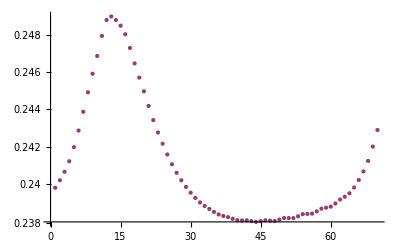

```mathematica
ListLogPlot[{Max/@Flatten/@Transpose[vx],√(Mean/@((Flatten/@Transpose[vz])^2))}]
```

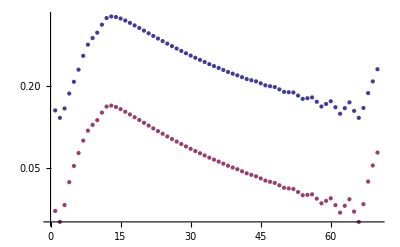

```mathematica
k
```

```mathematica
helicity=Total[MapThread[Times,{Take[out,3],rotd[Sequence@@Take[out,3],ghost]}]];
```

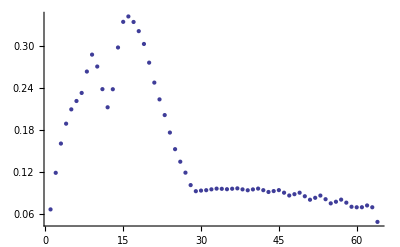

```mathematica
ListPlot[WithoutFict[Max/@Transpose[helicity]]]
```

```mathematica
phi=Outer[ArcTan,coor[[1]],coor[[3]]];
vphi=Table[vx[[All,ny,All]]Sin[phi]-vz[[All,ny,All]]Cos[phi],{ny,Dimensions[vx][[2]]}];
vrho=Table[vx[[All,ny,All]]Cos[phi]+vz[[All,ny,All]]Sin[phi],{ny,Dimensions[vx][[2]]}];
```

```mathematica
PrintRange[Max/@Flatten/@Transpose[vy]]
```

```mathematica
Fit[Take[Transpose[{coor[[2]],Log/@Max/@Flatten/@vphi}],{10,19}],{1,z},z]
```

0.120886-0.0254404 z

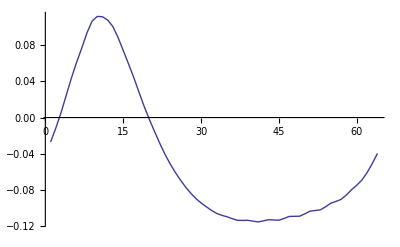

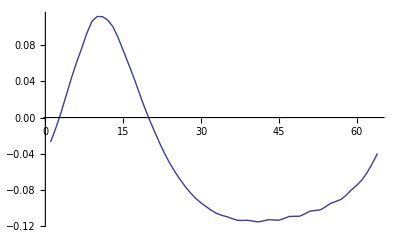

```mathematica
PrintRange[Log/@Max/@Flatten/@WithoutFict@vphi]
PrintRange[Log/@Max/@Flatten/@WithoutFict@vrho]
```

#### Графики сечений

```mathematica
DrawSection[Sequence@@Take[out,{2,4}-1],PointOfSections->{0.5,0,0}]
```

```mathematica
DrawSection[Bx,By,Bz,PointOfSections->{0.5,0,0}]
```

```mathematica
DrawSection[jx,jy,jz,PointOfSections->{0.5,0,0}]
```

```mathematica
PrintRange[WithoutFict@Bx⟦10,All,25⟧]
```

```mathematica
PrintRange[Take[Abs@Fourier@WithoutFict@Bx⟦15,All,15⟧,10]]
```

```mathematica
ReadDrawSection["dynamo_2_12820.snp",Binary,8,{5,6,7}]
```

```mathematica
DrawSection[Sequence@@ReadSection[4314]]
```

```mathematica
Table[ListPlot3D[Cut3D[Az,2,i],PlotRange->All],{i,1,Dimensions[By][[2]]}]
```

#### Чтение вдоль снэпов

```mathematica
ReadSection[iter_,fluct_:False]:=Block[{dump,str=ToString[iter],Ax,Ay,Az},
(*While[StringLength[str]<5,str="0"<>str];*)
(*dump=.;ReadBinarySnapFiles["dynamo_","_"<>str<>".snp",5,dump,PrintInfo->None];*)
dump=.;ReadBinarySnapFile["screw_32_"<>str<>".snp",6,dump,PrintInfo->None];
dump=Take[dump,{1,-1}];
(*Return[Take[dump,3]];*)
If[!NameQ[coor]∨Length[coor]=!=3,{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0},ProcDistrib->{4,2,4},NumberOfRefs->4]];
{Ax,Ay,Az}=Take[dump,-3];
If[fluct,
{Ax,Ay,Az}-=Transpose[Table[coor⟦1,i⟧Cos[coor⟦2,j⟧]{Sin[coor⟦2,j⟧],Cos[coor⟦2,j⟧],0},{i,1,n1+2ghost},{j,1,n2+2ghost},{k,1,n3+2ghost}],{2,3,4,1}]];
{Bx,By,Bz}=rotd[Ax,Ay,Az,ghost];
(*{jx,jy,jz}=rotc[Bx,By,Bz,ghost];*)
Return[{Bx,By,Bz}];];
```

```mathematica
grtot={};
```

```mathematica
nameexp="parker";
```

```mathematica
Block[{g,dump},dump=ReadList["runtest1.dmp"];np=dump⟦3⟧;KolProc=Times@@np;dump=Drop[dump,{3}];{t,count,n1,n2,n3,Rey}=Take[dump,6];dump=Drop[dump,6];{pm,vxm,vym,vzm,Axm,Aym,Azm,nutm}=Transpose[Partition[dump,8]];ghost=(Total[(Last[Dimensions[#1]]&)/@CutList[pm,Last[np]]]-n3)/(2 Last[np]);coor=ReadList["coord",Number,RecordLists->True];bounds=({1/2 (#1⟦ghost⟧+#1⟦ghost+1⟧),1/2 (#1⟦-ghost⟧+#1⟦-ghost-1⟧)}&)/@coor;Ax=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Axm,{1,2,3}]];Ay=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Aym,{1,2,3}]];Az=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Azm,{1,2,3}]];{Ax,Ay,Az}-=Transpose[Table[coor⟦1,i⟧ Cos[coor⟦2,j⟧] {Sin[coor⟦2,j⟧],Cos[coor⟦2,j⟧],0},{i,1,n1+2 ghost},{j,1,n2+2 ghost},{k,1,n3+2 ghost}],{2,3,4,1}];{Bx,By,Bz}=rotc[Ax,Ay,Az,ghost];{jx,jy,jz}=rotc[Bx,By,Bz,ghost];{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=GraphicsRow[{SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]]},Spacings->Scaled[0.],PlotLabel->"t="<>ToString[t]];
fname=nameexp<>"0000.gif";
Export[fname,g,ImageResolution->300,ImageSize->640];]
```

```mathematica
ReadSectionDraw2File[8896]
```

```mathematica
ReadSectionDraw2File[iter_]:=Block[{fname},
{Bx,By,Bz}=ReadSection[iter];
g1=DrawSection[Bx,By,Bz];
fname="screw"<>ToString[iter]<>"_B.gif";
Export[fname,g1,ImageResolution->300,ImageSize->640];
]
```

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp"]]
```

{162,283,387,489,582,671,756,844,930,1016,1101,1186,1272,1361,1445,1531,1618,1705,1789,1873,1961,2047,2132,2220,2304,2390,2474,2560,2644,2731,2817,2902,2990,3075,3160,3246,3331,3418,3503,3589,3674,3759,3844,3930,4015,4101,4186,4272,4356,4441,4527,4611,4696,4783,4868,4954,5040,5125,5211,5296,5381,5467,5554,5640,5727,5813,5899,5985,6068,6155,6241,6325,6411,6497,6582,6668,6753,6838,6924,7009,7094,7179,7265,7349,7434,7519,7602,7687,7772,7858,7943,8028,8113,8199,8282,8366,8451,8535,8620,8705,8760}

```mathematica
ReadSection[nums[[1]]]//Dimensions
```

{3,70,38,70}

```mathematica
infos=ScanSnaps;
```

Сетка одинаковая: {64,32,64}

Деление на процессы одинаковое: {4,2,4}

Структура у всех одинаковая

```mathematica
infos[[1]]
```

```mathematica
PrintRange[Sort@infos[[All,3]]]
```

```mathematica
lf1=lf2=lf3=lf4=lf5={};
Monitor[Do[Block[{Bx,By,Bz,g1,g2,fname},
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
(*Print["have read ponom_"<>ToString[nums⟦i⟧]<>".snp"];*)
AppendTo[lf1,Fourier@WithoutFict@Bx⟦15,All,15⟧];
AppendTo[lf2,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@Bx,{2,1,3}])];
AppendTo[lf3,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@By,{2,1,3}])];AppendTo[lf4,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@Bz,{2,1,3}])];
],{i,1,Length[nums]}],nums⟦i⟧];
```

```mathematica
Manipulate[ListLogPlot[Take[Abs@lf1⟦i⟧,15],PlotRange->{10^-20,10^5},PlotLabel->infos[[i]]],{i,1,Length[nums],1}]
```

```mathematica
Monitor[Do[Block[{Bx,By,Bz,jx,jy,jz,g1,g2,fname},
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
(*{jx,jy,jz}=rotc[Bx,By,Bz,3];*)
(*Print["have read ponom_"<>ToString[nums⟦i⟧]<>".snp"];*)
g1=DrawSection[Bx,By,Bz];
fname="screw"<>ToString[nums⟦i⟧]<>"_B.gif";
Export[fname,g1,ImageResolution->300,ImageSize->640];
(*g2=DrawSection[jx,jy,jz];
fname="ponom"<>ToString[nums⟦i⟧]<>"_j.gif";
Export[fname,g2,ImageResolution->300,ImageSize->640];*)
],{i,1,Length[nums]}],nums⟦i⟧];
```

```mathematica
res={};Monitor[Do[AppendTo[res,ReadSection[nums⟦i⟧,nproc]],{i,Length[nums]}],nums⟦i⟧]
```

```mathematica
Dimensions[res]
```

{400,3,38,38,38}

```mathematica
Do[Block[{g},
temp=First[Import["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp.ZIP",{"*.snp","Binary"}]];
Export["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp",temp,"Binary","DataFormat"-> "Byte"];
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
Print["have read dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
Close["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
DeleteFile["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
(*{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity,PlotLabel->"t="<>ToString[t]];*)
g=DrawSection[Bx,By,Bz];
fname="dynamo"<>ToString[nums⟦i⟧]<>".gif";Export[fname,g,ImageResolution->300,ImageSize->640];],{i,1,Length[nums]}];
```

```mathematica
Do[Block[{g},
temp=First[Import["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp.ZIP",{"*.snp","Binary"}]];
Export["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp",temp,"Binary","DataFormat"-> "Byte"];
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
Print["have read dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
Close["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
DeleteFile["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
(*{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity,PlotLabel->"t="<>ToString[t]];*)
g=DrawSection[Bx,By,Bz];
fname="dynamo"<>ToString[nums⟦i⟧]<>".gif";Export[fname,g,ImageResolution->300,ImageSize->640];],{i,1,Length[nums]}];
```

```mathematica
gr=Table[{Bx,By,Bz,jx,jy,jz}=ReadSection[i];{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity],{i,10,2820,10}];
```

```mathematica
grtot=First/@gr
```

```mathematica
Export["current.gif",Show[#,DisplayFunction->Identity]&/@gr,ConversionOptions->{"AnimationDisplayTime"->0.2},ImageResolution->300,ImageSize->640];
```

#### Сложное рисование поверхностей

```mathematica
{cont1, cont2} = (0.1*{Max[#1], Min[#1]} & )[By]
```

```mathematica
bounds
```

```mathematica
cubic=Table[Block[{r=√(x^2+y^2),f=ArcTan[y,x+10^-10]+π},If[z≤bounds⟦3,2⟧∧z≥bounds⟦3,1⟧∧r≤bounds⟦1,2⟧∧r≥bounds⟦1,1⟧,Byi[r,f,z],0]],{z,-1.5,1.5,0.2},{x,-6,6,0.2},{y,-6,6,0.2}];
```

```mathematica
g1 = ColorLighting[ListContourPlot3D[cubic, Contours -> {cont1}, DisplayFunction -> Identity], {1, 0, 0}];
g2 = ColorLighting[ListContourPlot3D[cubic, Contours -> {cont2}, DisplayFunction -> Identity], {0, 0, 1}];
```

```mathematica
Show[g1, Lighting -> Automatic]
```

```mathematica
Show[Graphics3D[EdgeForm[]], g1, g2, Lighting -> None]
```

```mathematica
Show[Graphics3D[EdgeForm[]], ColorLighting[ListContourPlot3D[cubic, Contours -> {cont1}, DisplayFunction -> Identity], {1, 0, 0}], ColorLighting[ListContourPlot3D[cubic, Contours -> {cont2}, DisplayFunction -> Identity], {0, 0, 1}], Lighting -> None]
```

#### Простое рисование поверхностей

```mathematica
{min,max}={Max[#],Min[#]}&@helicity
```

{1.83789,-0.0597603}

```mathematica
val=By^2+Bx^2+Bz^2;
mx = Max[Abs@val]
{min,max}=mx{-1,1};
```

0.0000620332

```mathematica
val=out[[2]];
mx = Max[Abs@val]
{min,max}={0,mx};
```

1.49676

```mathematica
gh = ListContourPlot3D[Transpose[val,{3,2,1}], Contours ->(min+max)/2+(max-min)/2 1/4{-1/2,1/2} , ContourStyle -> {Directive[Yellow, Opacity[0.8]], Directive[Pink, Opacity[0.8]]}, BoxRatios -> Automatic, Mesh -> False, AxesLabel -> {x, y, z}, DataRange -> bounds]
```

#### Просмотр массива типа ячеек и отражений

```mathematica
{node} = ReadAuxFiles[{"node"}];
```

```mathematica
Union[Flatten[node]]
```

```mathematica
coor[[1]]
```

```mathematica
ArrayPlot[Transpose[Map[BitAnd[Round[#1], 31] &, node, {2}]], FrameTicks -> True, Mesh -> True, Frame -> True]
```

```mathematica
flag = 8 + 64;
ListDensityPlot[Transpose[Map[BitAnd[Round[#1], flag] &, nm[[2]], {2}]]]
ListDensityPlot[Transpose[Map[BitAnd[Round[#1], flag] &, nm[[1]], {2}]]]
```

```mathematica
gc=Graphics[Circle[{n1/2+ghost,n1/2+ghost},n1/2]]
```

```mathematica
DisplayTogether[ListContourPlot[node], gc];
```